# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
f[{a_,b_}]:=Quiet[StringReplace[ToString[TeXForm[NumberForm[SetAccuracy[a±b,Accuracy[SetPrecision[b,2]]],ExponentFunction->(Null&)]]],"."->","]]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Fe-Ni 1.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

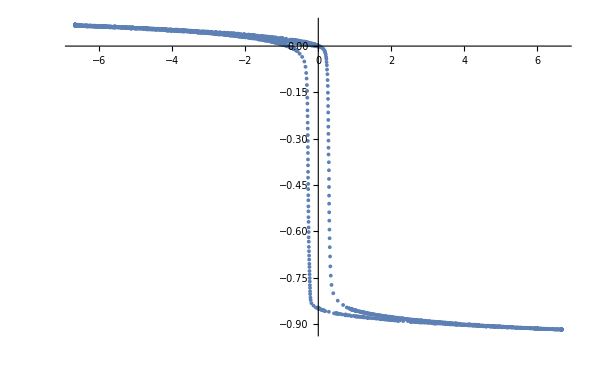

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=605;
d=(da+di)/2;
R=67.8;
```

```mathematica
dR=0.016*R+0.3
```

1.3848

```mathematica
N2=80;
A=h (da-di)/2;
messbereich=100;
fullfaktor=0.9;
```

```mathematica
dataProcessed={-N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

-0.0118349

-0.981481

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

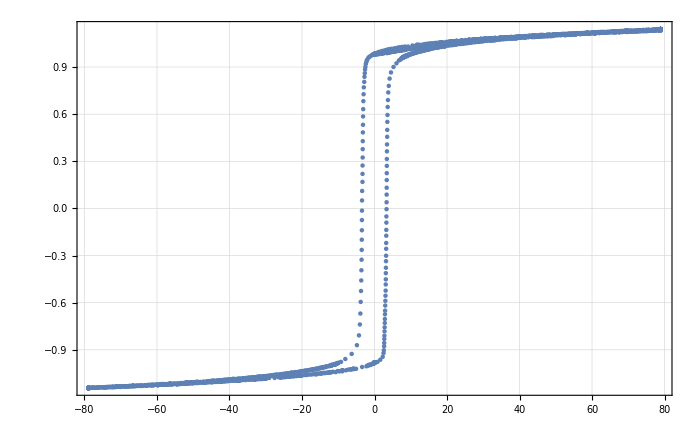

```mathematica
ListPlot[dataShifted,pltsettings]
```

## Remanence & Coercivity

```mathematica
sortedx=SortBy[dataShifted,Abs[Last[#]]&];
```

```mathematica
reg1data=DeleteCases[sortedx,x_/;x[[1]]<0][[1;;10]];
fit1=LinearModelFit[reg1data,x,x];
pars1=ungewichteterReg[reg1data[[All,1]],reg1data[[All,2]]];
reg2data=DeleteCases[sortedx,x_/;x[[1]]>0][[1;;10]];
fit2=LinearModelFit[reg2data,x,x];
pars2=ungewichteterReg[reg2data[[All,1]],reg2data[[All,2]]];
```

```mathematica
sortedy=SortBy[dataShifted,Abs[First[#]]&];
```

```mathematica
reg3data=DeleteCases[sortedy,x_/;x[[2]]<0][[1;;60]];
fit3=LinearModelFit[reg3data,x,x];
pars3=ungewichteterReg[reg3data[[All,1]],reg3data[[All,2]]];
reg4data=DeleteCases[sortedy,x_/;x[[2]]>0][[1;;30]];
fit4=LinearModelFit[reg4data,x,x];
pars4=ungewichteterReg[reg4data[[All,1]],reg4data[[All,2]]];
```

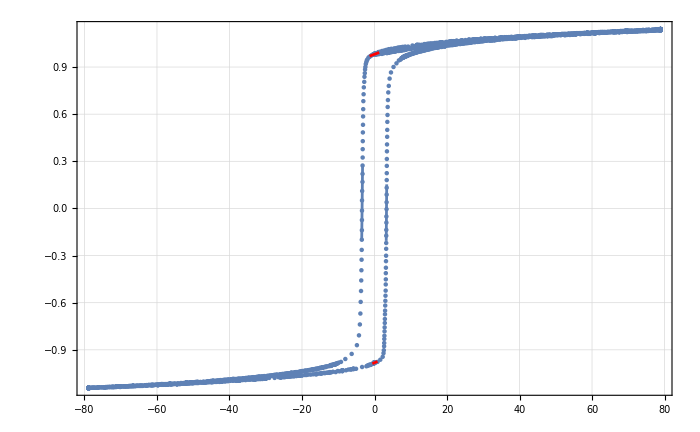

```mathematica
Show[ListPlot[dataShifted],Plot[fit1[x],{x,Min[reg1data[[All,1]]],Max[reg1data[[All,1]]]}],Plot[fit2[x],{x,Min[reg2data[[All,1]]],Max[reg2data[[All,1]]]}],Plot[fit3[x],{x,Min[reg3data[[All,1]]],Max[reg3data[[All,1]]]},PlotStyle->Red],Plot[fit4[x],{x,Min[reg4data[[All,1]]],Max[reg4data[[All,1]]]},PlotStyle->Red],pltsettings]
```

```mathematica
pltHeights=0.4;
```

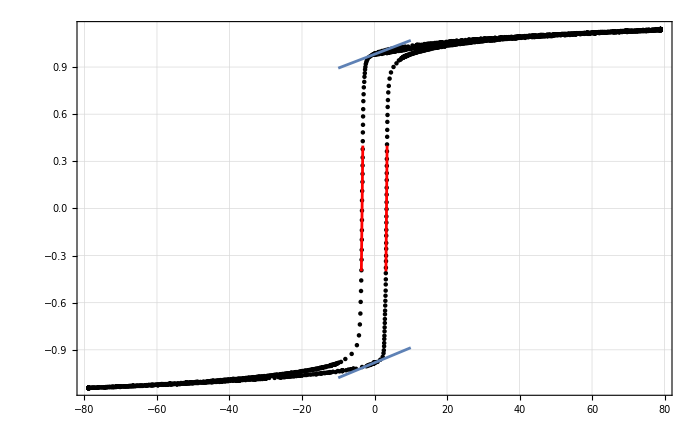

```mathematica
Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-10,10}],Plot[fit4[x],{x,-10,10}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/ni-fe 5000H2.pdf",Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-10,10}],Plot[fit4[x],{x,-10,10}],pltsettings],Background->None];
```

## Remance and coercitivity

```mathematica
Brp=pars3[[1]]
dBrp=pars3[[3]]
Brm=pars4[[1]]
dBrm=pars3[[3]]
```

0.981356

0.000343704

-0.982194

0.000343704

```mathematica
Hm=pars2[[1]]/pars2[[2]]
```

3.42582

```mathematica
(*dHm=Abs[pars2[[1]]/pars2[[2]]]Sqrt[(pars2[[3]]/pars2[[1]])^2 +(pars2[[4]]/pars2[[2]])^2 ]*)
```

```mathematica
Hp=pars1[[1]]/pars1[[2]]
```

-3.31244

```mathematica
(*dHp=Abs[pars1[[1]]/pars1[[2]]]Sqrt[(pars1[[3]]/pars1[[1]])^2 +(pars1[[4]]/pars1[[2]])^2 ]*)
```

### New Computations

```mathematica
dHm=Hm*dR/R
```

0.0699716

```mathematica
dHp=Abs[Hp]*dR/R
```

0.0676559

```mathematica
f[{Hm, dHm}]
f[{Hp, dHp}]
```

3,426\pm 0,070

-3,312\pm 0,068

```mathematica
Hbest=(Abs[Hm]+Abs[Hp])/2;
```

```mathematica
dHbest=Max[{Abs[Hbest-(Abs[Hm]-dHm)],Abs[Hbest-(Abs[Hm]+dHm)],Abs[Hbest-(Abs[Hp]-dHp)],Abs[Hbest-(Abs[Hp]+dHp)]}]
```

0.12666

```mathematica
f[{Hbest,dHbest}]
```

3,37\pm 0,13

```mathematica
extractedB=DeleteCases[dataShifted,x_/;Abs[x[[1]]]>dHbest]
```

{{0.118349,0.98129},{0.118349,0.981394},{0.118349,0.980058},{0.118349,0.982005},{0.118349,0.983796},{0.0946792,0.982061},{0.0828443,0.986111},{0.0946792,0.981581},{0.106514,0.983644},{0.118349,0.982341},{0.118349,0.983796},{0.118349,0.982106},{0.0946792,0.983796},{0.0828443,0.981651},{0.0828443,0.983576},{0.0828443,0.981637},{0.0710094,0.983576},{0.0710094,0.981838},{0.0710094,0.983573},{0.0710094,0.981928},{0.0710094,0.983157},{0.0828443,0.981035},{0.0710094,0.983796},{-0.0118349,0.980821},{-0.0828443,0.981894},{-0.0946792,0.979306},{-0.106514,0.98177},{-0.106514,0.979481},{-0.118349,0.981951},{-0.118349,0.979707},{-0.118349,0.981513},{-0.118349,0.979642},{-0.118349,0.980569},{-0.118349,0.979167},{-0.118349,0.981281},{-0.118349,-0.983796},{-0.118349,-0.983796},{-0.0828443,-0.981481},{0.0591745,-0.981481},{0.0946792,-0.979167},{0.0946792,-0.981481},{0.106514,-0.979167},{0.106514,-0.981481},{0.118349,-0.979167},{0.118349,-0.981481}}

```mathematica
dBrp=(Max[#]-Min[#]&)[DeleteCases[extractedB,x_/;x[[2]]<0][[All,2]]]
```

0.00694444

```mathematica
dBrm=(Max[#]-Min[#]&)[DeleteCases[extractedB,x_/;x[[2]]>0][[All,2]]]
```

0.00462963

```mathematica
BBest=(Abs[Brp]+Abs[Brm])/2;
```

```mathematica
f[{Brp, dBrp}]
f[{Brm, dBrm}]
```

0,9814\pm 0,0069

-0,9822\pm 0,0046

```mathematica
dBbest=Max[{Abs[BBest-(Abs[Brp]-dBrp)],Abs[BBest-(Abs[Brp]+dBrp)],Abs[BBest-(Abs[Brm]-dBrm)],Abs[BBest-(Abs[Brm]+dBrm)]}]
```

0.00736357

```mathematica
f[{BBest, dBbest}]
```

0,9818\pm 0,0074

### Average Values

```mathematica
NumberForm[(Brp/dBrp^2 +Abs@Brm/dBrm^2)/(1/dBrp^2 + 1/dBrm^2),10]
1/Sqrt[(1/dBrp^2 + 1/dBrm^2)]
```

0.9819365269

0.00385208

```mathematica
(Abs@Hp/dHp^2 +Hm/dHm^2)/(1/dHp^2 + 1/dHm^2)
Sqrt[1/(1/dHp^2 + 1/dHm^2)]
```

3.36722

0.048638

## Area

```mathematica
dataShifted[[1]]
```

{0.118349,0.98129}

```mathematica
poly=Polygon[Table[dataShifted[[i]],{i,1,Length[dataShifted],50}]]
```

Polygon[…]

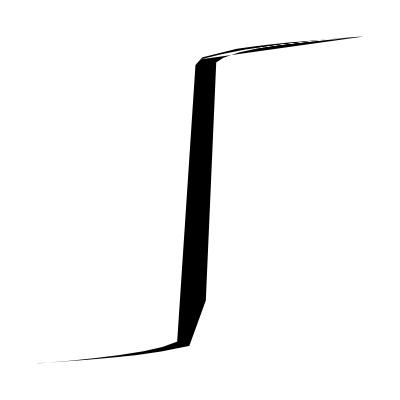

```mathematica
Graphics[poly,AspectRatio->1]
```

```mathematica
RegionMeasure[poly]
```

-24.4708

```mathematica
dat1=DeleteDuplicatesBy[SortBy[dataShifted[[200;;1100]],First],First];
dat2=DeleteDuplicatesBy[SortBy[dataShifted[[1100;;-1]],First],First];
```

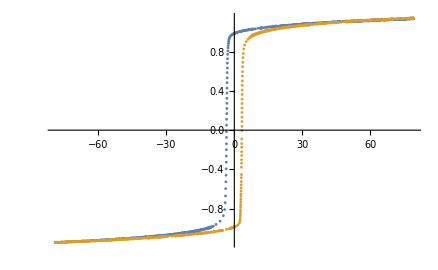

```mathematica
ListPlot[{dat1,dat2}]
```

```mathematica
f1=Interpolation[dat1,InterpolationOrder->1]
f2=Interpolation[dat2,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Integrate[f1[t],{t,-77.1,77.1}]-Integrate[f2[t],{t,-77.1,77.1}]
```

15.8288

```mathematica
dat1p={#[[1]](1-dR/R), #[[2]]}&/@dat1;
dat2p={#[[1]](1+dR/R), #[[2]]}&/@dat2;
```

```mathematica
f1p=Interpolation[dat1p,InterpolationOrder->1]
f2p=Interpolation[dat2p,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Integrate[f1p[t],{t,-77.1,77.1}]-Integrate[f2p[t],{t,-77.1,77.1}]
```

InterpolatingFunction::dmvali: The integration endpoint -77.1 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

15.8171

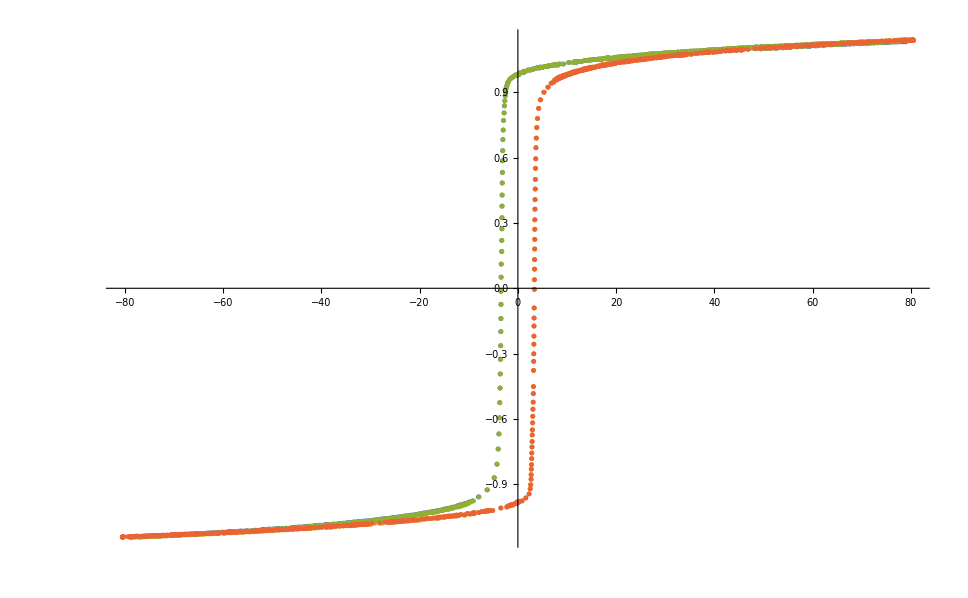

```mathematica
ListPlot[{dat1,dat2,dat1p,dat2p}]
```

```mathematica
15.818923470653893/(8250)
```

0.00191745

```mathematica
0.0019174452691701688*10^3
```

1.91745

```mathematica
dHbest
```

0.12666

```mathematica
yrange=(Max[#]-Min[#])&[dataShifted[[All,2]]]
```

2.28704

```mathematica
2*yrange*dHbest/8250*10^3
```

0.0702244